# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[ParentDirectory[NotebookDirectory[]]]],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","SemiConstrained","Constrained","ConstrainedCorrelation"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

iaa=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ibb=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
iccolor=reduire[clean@Import[pathResult],reduce];

Show[iaa]
```

-Graphics-

## Image sections

```mathematica
dims=(*{828,282}*){400,200}
```

{400,200}

```mathematica
ims=Table[

tim=1;

nx=1+dims[[1]]*tim*i;
ny=1+dims[[2]]*tim*j;

{ia,ib,icolor}=ImageTake[#,{ny,ny+dims[[2]]*tim},{nx,nx+dims[[1]]*tim}]&/@{iaa,ibb,iccolor}

,{j,Range[1,1]},{i,Range[1,1]}]
```

{{{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
ims=Flatten[ims,1];
```

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],minmax[[2]],minmax,Range[1,1+dims[[1]]*tim,steps],Range[1,1+dims[[2]]*tim],e,"ConstrainedCorrelation"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,1+dims[[2]]*tim}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,1+dims[[2]]*tim}];

(* We create g0 *)
g0=Graphics[{PointSize[0.003],Table[affiche[#,1+dims[[2]]*tim-y]&/@realPVTable[[y]],{y,1,1+dims[[2]]*tim}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Run

```mathematica
(* Test values *)
levels={{1,4}};
dis=0.1;
e=0.001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating initial values *)
v0Range={0,2};
r=Random[];
listv0=Select[RandomReal[v0Range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[v0Range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-30];
```

```mathematica
(* Creating condition *)
topbot={0,2};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Scaling results *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
solution=bigTest[steps,n,u,listv0,condition,e,levels,ims];
```

```mathematica
(*selectrion criteria, level, image, extra, kind of result, rows *)
Dimensions[solution]
```

{1,1,4}

### Images

```mathematica
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}],LegendMarkerSize->100]
```

```mathematica
imagesTable=Table[

ConformImages[Rasterize[Image[#],ImageResolution->400]&/@Flatten[{ims[[which,1;;2]],solution[[which,1,4]]}],{900}]

,{which,Length[ims]}]

imFinal=Legended[Grid[imagesTable],legendBar]
```

{{-Graphics-,-Graphics-,-Graphics-}}

-Graphics- | -Graphics- | -Graphics-

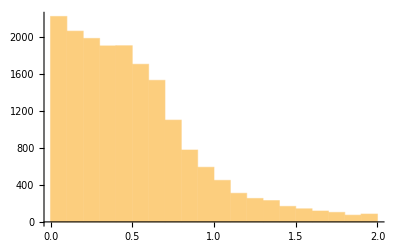

0.507858

0.391098

```mathematica
Histogram[Flatten[solution[[1,1,1,All,All,2]]]]
Mean[Flatten[solution[[1,1,1,All,All,2]]]]
StandardDeviation[Flatten[solution[[1,1,1,All,All,2]]]]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"fullSintelDataset"}];
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\synaereal-clean-Full-lvls-im.pdf

### Histogram Grid 1

```mathematica
Histogram[Flatten[solution[[1,1,1,All,All,2]]]]
```

-Graphics-

```mathematica
fontsize=30;
imagesize=500;
maxvalue={{0,2},{0,50000}};
bar={10,20,30};
```

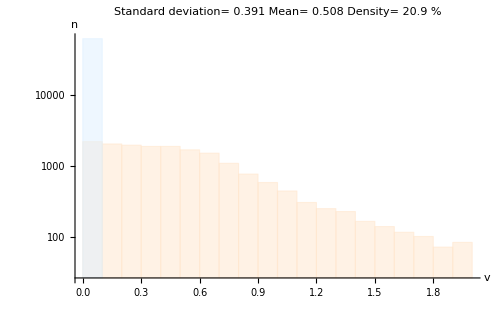

```mathematica
histogramGrid=
Table[

convergedData=Flatten[solution[[idxims,1,1,All,All,2]]];
okData=Flatten[solution[[idxims,1,2,All,All,2]]];
nonConvergedData=Flatten[solution[[idxims,1,3,All,All,2]]];

std=StandardDeviation[convergedData];
mu=Mean[convergedData];
density=((Length[Flatten[DeleteDuplicates[#]&/@Round[solution[[idxims,1,1,All,All,1]]]]])/((1.+dims[[1]]*tim)*(1.+dims[[2]]*tim)))*100;

Histogram[{convergedData, nonConvergedData},20,"LogCount",
PlotLabel->Column[{
Style[Row[{"Standard deviation= ",NumberForm[std,3]}],FontSize->fontsize,FontFamily->"Times",Italic],
Style[Row[{"Mean= ",NumberForm[mu,3]}],FontSize->fontsize, FontFamily->"Times",Italic],
Style[Row[{"Density= ",NumberForm[density,3]," %"}],FontSize->fontsize, FontFamily->"Times",Italic]},
Spacings->0.1,
Alignment->Center],
PlotRange->maxvalue,
ImageSize->imagesize,
AxesLabel->{Style["v",FontSize->fontsize,FontFamily->"Times",Italic],Style["n",FontSize->fontsize,FontFamily->"Times",Italic]},ChartStyle->{LightOrange,LightBlue,LightGreen},TicksStyle->fontsize-6]
,{idxims,Length[ims]}]
```

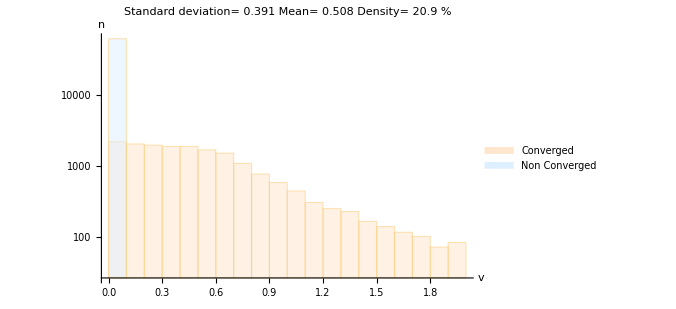

```mathematica
hFinal=Legended[
histogramGrid[[1]],
Placed[SwatchLegend[{LightOrange, LightBlue, LightGreen},{Style["Converged",FontSize->fontsize, FontFamily->"Times",Italic], Style["Non Converged",FontSize->fontsize, FontFamily->"Times",Italic]},LegendLayout->"Row"],Below]]
```

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
Export[FileNameJoin[{figsDirectory,nbname<>"-hist.pdf"}],hFinal, ImageResolution->300]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\fullSintelDataset\synaereal-clean-Full-lvls-hist.pdf